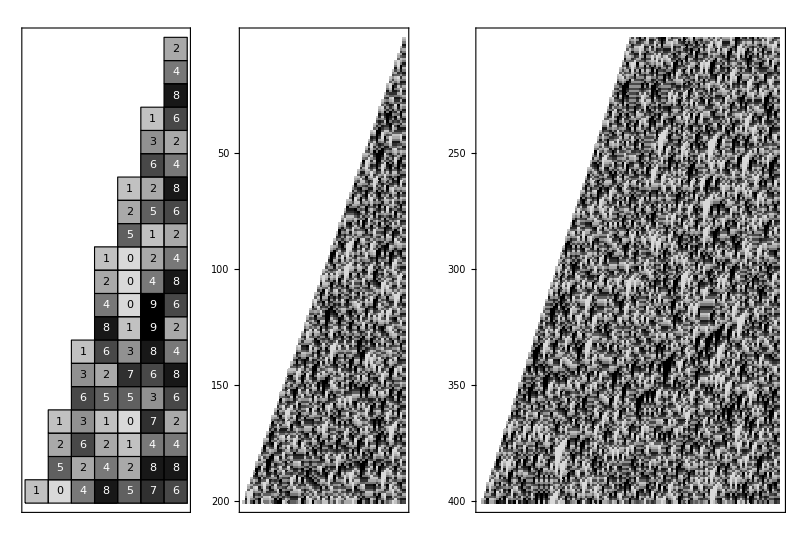

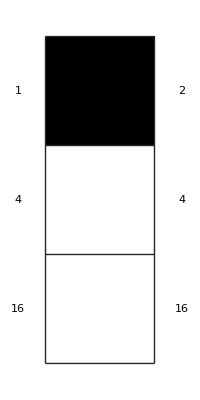
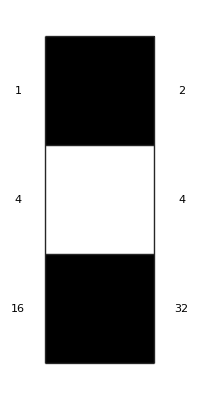
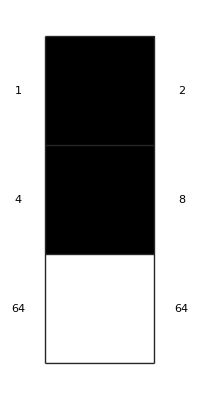
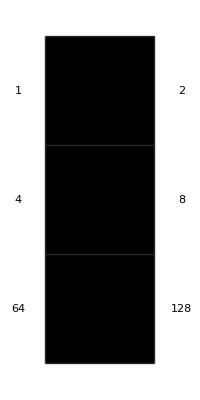
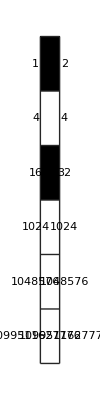
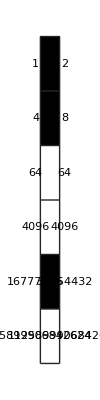
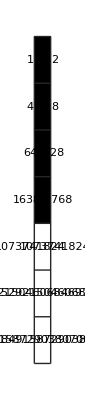

```mathematica
GraphicsRow@Table[ResourceFunction["RaggedDigitsPlot"][IntegerDigits[2^Range@@range],10,"Label"->range[[2]]<=20,Mesh->range[[2]]<=20,],{range,{{1,20},{0,200},{200,400}}}]

Column[Row[#,Spacer[45]]&/@TakeList[Framed@Show[{ArrayPlot[{IntegerDigits[#,2]}//Transpose,],Graphics[Module[{b=IntegerDigits[#,2],n=1},MapIndexed[{n=n^2;Text[n,{-.25,Length[b]-First[#2]+.5},{1,0}],If[#1==1,n*=2];Text[n,{1.25,Length[b]-First[#2]+.5},{-1,0}]}&,b]]]},]&/@{4,5,6,7,40,50,120},{4,2,1}]]
```